In this notebook I integrate the expression from the PDG document FORM FACTORS FOR RADIATIVE PION AND KAON DECAYS.

```mathematica
ib[x_,y_]:=(1-y+r)/(x^2(x+y-1-r))(x^2+2(1-x)(1-r)-(2 x r(1-r))/(x+y-1-r))
sdp[x_,y_]:=(x+y-1-r)((x+y-1)(1-x)-r)
sdm[x_,y_]:=(1-y+r)((1-x)(1-y)+r)
sintp[x_,y_]:=(1-y+r)/(x(x+y-1-r))((1-x)(1-x-y)+r)
sintm[x_,y_]:=(1-y+r)/(x(x+y-1-r))(x^2-(1-x)(1-x-y)-r)
d2Γdxdx[x_,y_]:=alphaem/(2π)Γ 1/(1-r)^2(ib[x,y]+1/r(mpi/(2fpi))^2((VPI+API)^2 sdp[x,y]+(VPI-API)^2 sdm[x,y])+mpi/fpi((VPI+API)sintp[x,y]+(VPI-API)sintm[x,y]))
```

```mathematica
ibyIndefInt[x_,y_]:=Integrate[alphaem/(2π)Γ 1/(1-r)^2 ib[x,yp],yp]/.yp->y
sdpyIndefInt[x_,y_]:=Integrate[alphaem/(2π)Γ 1/(1-r)^2 1/r(mpi/(2fpi))^2(VPI+API)^2 sdp[x,yp],yp]/.yp->y
sdmyIndefInt[x_,y_]:=Integrate[alphaem/(2π)Γ 1/(1-r)^2 1/r(mpi/(2fpi))^2(VPI-API)^2 sdm[x,yp],yp]/.yp->y
sintpyIndefInt[x_,y_]:=Integrate[alphaem/(2π)Γ 1/(1-r)^2 mpi/fpi(VPI+API)sintp[x,yp],yp]/.yp->y
sintmyIndefInt[x_,y_]:=Integrate[alphaem/(2π)Γ 1/(1-r)^2 mpi/fpi(VPI-API)sintm[x,yp],yp]/.yp->y
```

Integration region:
	(∫_(2 √r))^(1-x)ⅆy

```mathematica
ibyInt[x_]:=ibyIndefInt[x,1-x]-ibyIndefInt[x,2 √r]//Simplify;
sdpyInt[x_]:=sdpyIndefInt[x,1-x]-sdpyIndefInt[x,2 √r]//Simplify;
sdmyInt[x_]:=sdmyIndefInt[x,1-x]-sdmyIndefInt[x,2 √r]//Simplify;
sintpyInt[x_]:=sintpyIndefInt[x,1-x]-sintpyIndefInt[x,2 √r]//Simplify;
sintmyInt[x_]:=sintmyIndefInt[x,1-x]-sintmyIndefInt[x,2 √r]//Simplify;
```

```mathematica
dΓdx[x_]=ibyInt[x]+sdpyInt[x]+sdmyInt[x]+sintpyInt[x]+sintmyInt[x]//Simplify[#,Assumptions->{1>r>0}]&;
```

```mathematica
dΓdxSimp1[x_]=1/(48 π (-1+r)^2)alphaem Γ (-1/(fpi^2 r)mpi^2 (API+VPI)^2 (12 r^(5/2)+3 r (-10+x) (-1+x)^2-12 √r (-1+x)^3-2 (-1+x)^4+6 r^2 (-5+3 x)+4 r^(3/2) (10-13 x+3 x^2))-1/(fpi^2 r)mpi^2 (API-VPI)^2 (12 r^(5/2)+r^(3/2) (40-28 x)-12 √r (-1+x)+6 r^2 (-5+3 x)-3 r (10-9 x-2 x^2+x^3)+2 (-1+x+x^3-x^4))+1/(fpi x)12 mpi (API+VPI) (-1+4 √r-6 r+4 r^(3/2)+x-4 √r x+6 r x+x^2-x^3+2 r x^2 Log[r/(1-2 √r+r-x)])+1/(fpi x)12 mpi (API-VPI) (-1+4 √r-6 r+4 r^(3/2)+x-4 √r x+6 r x+3 x^2-4 √r x^2-3 x^3+2 (r-x) x^2 Log[r/(1-2 √r+r-x)])+1/x^2 24 (2 (-1+r) x^2-(2 (-1+r) r x^2)/(1-2 √r+r-x)+r (2+2 r (-1+x)-2 x+x^2)-(1-2 √r+r-x) (2+2 r (-1+x)-2 x+x^2)+x (2-2 r^2-2 x+2 r x+x^2) Log[r/(1-2 √r+r-x)]));
```

```mathematica
eμ=(√(mμ^2+kν^2)/.Solve[√(mμ^2+kν^2)+kν==mπ,kν])⟦1⟧//Simplify;
```

```mathematica
Solve[eμ==√(me^2+k^2)+k,k]/.{mμ->105.,mπ->135.,me->0.5}
```

{{k→54.1655}}

```mathematica
Solve[mπ==√(ml^2+k^2)+k,k]//Simplify
%/.ml->me/.{mμ->105.,mπ->135.,me->0.5}
```

{{k→(mπ^2-ml^2)/(2 mπ)}}

{{k→67.4991}}

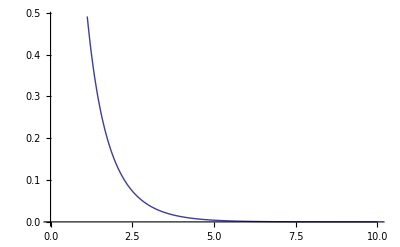

```mathematica
Plot[BesselK[1,x],{x,0,10}]
```